## First define the generator base

```mathematica
Table[
With[
{sets=ConnectedComponents[ GraphComplement[allGraphs5[k,"graph"]]]},
allGraphs5[k,"colofourgenerator"]=PartitionToSymbol[sets,"g"]
],
{k,allGraphs5GeneratorAtomKeys}
]
```

{g1x2x3x4x5,g1x2x3x45,g1x2x34x5,g1x2x35x4,g1x23x4x5,g1x24x3x5,g1x25x3x4,g12x3x4x5,g13x2x4x5,g14x2x3x5,g15x2x3x4,g1x23x45,g1x24x35,g1x25x34,g12x3x45,g12x34x5,g12x35x4,g13x2x45,g13x24x5,g13x25x4,g14x2x35,g14x23x5,g14x25x3,g15x2x34,g15x23x4,g15x24x3,g1x2x345,g1x234x5,g1x235x4,g1x245x3,g123x4x5,g124x3x5,g125x3x4,g134x2x5,g135x2x4,g145x2x3,g12x345,g123x45,g124x35,g125x34,g13x245,g134x25,g135x24,g14x235,g145x23,g15x234,g1x2345,g1234x5,g1235x4,g1245x3,g1345x2,g12345}

```mathematica
repFullToGen=ToRules[
Reduce[
Table[
allGraphs5[k,"colofourgenerator"]==allGraphs5[k,"colofour"]
,
{k,allGraphs5GeneratorAtomKeys}
],
Table[allGraphs5[k,"colofour"],{k,allGraphs5AtomKeys}]
]
];
```

```mathematica
Monitor[
Table[
allGraphs5[k,"colofourgenerator"]=Simplify[allGraphs5[k,"colofour"]/.repFullToGen],
{k,Sort[Keys[allGraphs5]]}
],k]
```

{g12345,1893,g12345-g1234x5-g1235x4-g123x45+2 g123x4x5-g1245x3-g124x35+2 g124x3x5-g125x34+2 g125x3x4-g12x345+2 g12x34x5+2 g12x35x4+2 g12x3x45-6 g12x3x4x5-g1345x2-g134x25+2 g134x2x5-g135x24+2 g135x2x4-g13x245+2 g13x24x5+2 g13x25x4+9+2 g14x25x3+2 g14x2x35-6 g14x2x3x5-g15x234+2 g15x23x4+2 g15x24x3+2 g15x2x34-6 g15x2x3x4-g1x2345+2 g1x234x5+2 g1x235x4+2 g1x23x45-6 g1x23x4x5+2 g1x245x3+2 g1x24x35-6 g1x24x3x5+2 g1x25x34-6 g1x25x3x4+2 g1x2x345-6 g1x2x34x5-6 g1x2x35x4-6 g1x2x3x45+24 g1x2x3x4x5}
 |  |  |  |

## Add Knuth

```mathematica
KnuthRep[sets_]:=Block[{result=Range[Length[Flatten[sets]]], currentBlock, block, item},
For[currentBlock=1,currentBlock≤Length[sets],currentBlock++,
block=sets[[currentBlock]];
For[item=1,item≤Length[block],item++,
result[[block[[item]]]]=currentBlock
]
];
result
]
```

```mathematica
KnuthRep[allGraphs5[alfa1Key,"vertexsets"]]
```

{1,2,1,2,3}

```mathematica
allGraphs5[1,"vertexsets"]
```

{{1},{2},{3},{4},{5}}

```mathematica
KnutComp[s1_,s2_]:=Block[{v1=SymbolToSets[s1],v2=SymbolToSets[s2]},
Return[FromDigits[v1,Length[v1]]≤FromDigits[v2,Length[v2]]]
]
```

## Now define the base basic data

```mathematica
Bases=Association[];
```

```mathematica
Bases["C"]=Association[];
```

```mathematica
Bases["C","Colofour"]="colofour";
```

```mathematica
Bases["E"]=Association[];
```

```mathematica
Bases["E","Colofour"]="colofourrealnull";
```

```mathematica
Bases["G"]=Association[];
```

```mathematica
Bases["G","Colofour"]="colofourgenerator";
```

```mathematica
Bases["F"]=Association[];
```

```mathematica
Bases["F","Colofour"]="colofournull";
```

```mathematica
allBases={"C","E","G","F"}
```

{C,E,G,F}

## Compute keys and variables

```mathematica
MyComp:=CompareSymbols;
```

```mathematica
Table[Bases[base,"AtomKeys"]=Sort[Select[Keys[allGraphs5],Length[ListofVars[allGraphs5[#,Bases[base,"Colofour"]]]]==1&],MyComp[allGraphs5[#1,Bases[base,"Colofour"]],allGraphs5[#2,Bases[base,"Colofour"]]]&]
,{base,allBases}];
```

```mathematica
Table[Bases[base,"Variables"]=Table[allGraphs5[k,Bases[base,"Colofour"]],{k,Bases[base,"AtomKeys"]}]
,{base,allBases}];
```

```mathematica
BaseCoeff[key_,base_]:=Table[Coefficient[allGraphs5[key,Bases[base,"Colofour"]],var],{var,Bases[base,"Variables"]}]
```

```mathematica
BaseCoeff[0,"E"]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
ConversionMatrix[base1_,base2_]:=Table[BaseCoeff[key1,base2],{key1,Bases[base1,"AtomKeys"]}]
```

```mathematica
Table[Bases[base,"AtomKeys"],{base,allBases}]//Flatten//DeleteDuplicates//Length
```

203

```mathematica
Clear[RepGraph];RepGraph[base_]:=RepGraph[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ShowGraph5Least[key],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepAtLeast];RepAtLeast[base_]:=RepAtLeast[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->allGraphs5[key,"atleast"],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
Clear[RepChromial];RepChromial[base_]:=RepChromial[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->ChromaticPolynomial[allGraphs5[key,"graph"],x],{key,Bases[base,"AtomKeys"]}]
```

## Checking some conversion matrix identities

```mathematica
ConversionMatrix["E","C"]==Transpose[ConversionMatrix["G","C"]]
```

True

```mathematica
ConversionMatrix["E","C"]==Inverse[ConversionMatrix["C","E"]]
```

True

```mathematica
ConversionMatrix["G","C"]==Transpose[Inverse[ConversionMatrix["C","E"]]]
```

True

```mathematica
Table[base->ConversionMatrix[base,base]==IdentityMatrix[52],{base,allBases}]
```

{C→True,E→True,G→True,F→True}

```mathematica
ConversionMatrix["F","C"]//SymmetricMatrixQ
```

True

```mathematica
Sort[DeleteDuplicates[Map[Mean[#]*52&,ConversionMatrix["F","C"]]]]
```

{1,5,13,17,27,37,52}

```mathematica
SymmetricMatrixQ[ConversionMatrix["C","F"]]
```

True

```mathematica
Det[ConversionMatrix["F","C"]]//FactorInteger
```

{{-1,1},{2,28},{3,6}}

## All vectors in a base are orthogonal

```mathematica
Table[Table[Table[BaseCoeff[k,base].BaseCoeff[l,base],{k,Bases[base,"AtomKeys"]}],{l,Bases[base,"AtomKeys"]}]==IdentityMatrix[52],{base,allBases}]
```

{True,True,True,True}

```mathematica
Table[
base->Sort[Tally[Table[Length[Select[Keys[allGraphs5],VertexCount[allGraphs5[#,"graph"]]==5&&BaseCoeff[k,base].BaseCoeff[#,base]==0&]],{k,Bases[base,"AtomKeys"]}]],#1[[2]]<#2[[2]]&]
,{base,allBases}]//TableForm
```

$Aborted

```mathematica
Table[
base->Sort[Tally[Table[Length[Select[Keys[allGraphs5],BaseCoeff[k,base].BaseCoeff[#,base]==0&]],{k,Bases[base,"AtomKeys"]}]],#1[[2]]<#2[[2]]&]
,{base,allBases}]//TableForm
```

C→{{1843,1},{871,1},{1801,5},{1757,10},{1663,10},{1319,10},{1567,15}}
E→{{671,1},{871,1},{1065,5},{1541,10},{1279,10},{1319,10},{1567,15}}
G→{{1843,1},{526,1},{1779,5},{1725,10},{1635,10},{1199,10},{1528,15}}
F→{{671,1},{1843,1},{692,5},{668,10},{767,10},{684,10},{824,15}}

## Viewing come COnversion matrices

```mathematica
Table[Det[ConversionMatrix[base1,base2]],{base1,allBases},{base2,allBases}]
```

{{1,1,1,-1/195689447424},{1,1,1,-1/195689447424},{1,1,1,-1/195689447424},{-195689447424,-195689447424,-195689447424,1}}

```mathematica
Table[base1->Det[ConversionMatrix[base1,base2]]//N,{base1,allBases},{base2,{"G"}}]
```

{{C→1.},{E→1.},{G→1.},{F→-1.95689×10^11}}

```mathematica
Tally[Table[Sort[Map[Length,allGraphs5[k,"vertexsets"]]],{k,allGraphs5AtomKeys}]]
```

{{{1,1,1,1,1},1},{{1,1,1,2},10},{{1,1,3},10},{{1,2,2},15},{{1,4},5},{{2,3},10},{{5},1}}

```mathematica
FactorInteger[195689447424]
```

{{2,28},{3,6}}

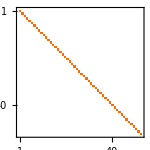
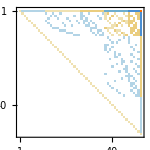
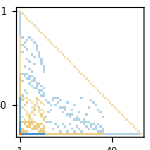
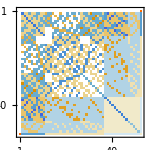
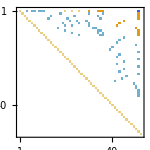
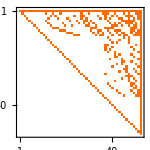
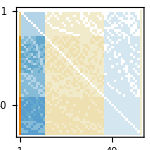
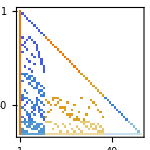
| C | E | G | F | T
C | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
F | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-
T | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
TableForm[Table[MatrixPlot[ConversionMatrix[base1,base2],ImageSize->150],{base1,allBases},{base2,allBases}],TableHeadings->{allBases, allBases},TableAlignments->{Center, Center}]
```

```mathematica
TableForm[Table[MatrixPlot[Inverse[ConversionMatrix[base1,base2]],ImageSize->150],{base1,allBases},{base2,allBases}],TableHeadings->{Reverse[allBases], Reverse[allBases]},TableAlignments->{Center, Center}]
```

| F | G | E | C
F | -Graphics- | -Graphics- | -Graphics- | -Graphics-
G | -Graphics- | -Graphics- | -Graphics- | -Graphics-
E | -Graphics- | -Graphics- | -Graphics- | -Graphics-
C | -Graphics- | -Graphics- | -Graphics- | -Graphics-

## Some play

```mathematica
AtLeast[base_]:=Table[allGraphs5[k,"atleast"],{k,Bases[base,"AtomKeys"]}]
```

```mathematica
AtLeast["C"]
```

{0,0,0,0,0,0,0,0,0,0,0,1,0,0,1,1,0,0,0,0,0,0,0,1,1,0,1,1,0,0,1,0,1,0,0,1,1,1,0,1,0,0,0,0,1,1,1,1,1,1,1,1}

```mathematica
AtLeast["E"]
```

{34,13,13,10,13,10,10,13,10,10,13,5,2,4,5,5,4,4,2,2,2,4,2,5,5,4,5,5,4,4,5,4,5,4,4,5,2,2,1,2,1,1,1,1,2,2,2,2,2,2,2,1}

```mathematica
AtLeast["C"].BaseCoeff[0,"C"]
```

21

```mathematica
BaseCoeff[K5Key,"C"].ConversionMatrix["C","E"].AtLeast["E"]
```

-2

```mathematica
Table[{allGraphs5[k,"atleast"],BaseCoeff[k,"C"].ConversionMatrix["C","E"].AtLeast["E"]},{k,allGraphs5AtomKeys}]
```

{{0,-2},{0,0},{0,1},{0,0},{1,1},{0,1},{0,1},{0,1},{0,0},{0,1},{0,0},{1,1},{0,1},{1,1},{1,1},{0,0},{1,1},{0,1},{1,1},{1,1},{0,1},{0,0},{0,0},{0,1},{0,0},{1,1},{1,1},{0,1},{0,1},{0,0},{0,0},{0,0},{0,1},{0,0},{0,1},{0,0},{1,1},{0,0},{1,1},{0,1},{1,1},{1,1},{1,1},{1,1},{0,1},{0,0},{1,1},{1,1},{1,1},{1,1},{1,1},{1,1}}

```mathematica
BaseCoeff[0,"C"]
```

{1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1}

```mathematica
Outer[Times,BaseCoeff[2278,"E"],AtLeast["E"]].ConversionMatrix["E","C"].BaseCoeff[2278,"C"]
```

{915,-915,-915,0,0,-915,0,0,0,-915,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,915,915,0,915,0,915,0,915,0,915,0,0,0,0,0,0,0,0,0,0,-915,-915,0,-915,-915,915}

```mathematica
ConversionMatrix["C","E"].AtLeast["E"]
```

{-2,0,0,1,0,1,1,0,1,1,0,1,0,1,1,1,1,1,0,0,0,1,0,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,0,1,0,0,0,0,1,1,1,1,1,1,1,1}

```mathematica
ConversionMatrix["E","C"].AtLeast["C"]
```

{21,11,11,6,11,6,6,11,6,6,11,5,2,3,5,5,3,3,2,2,2,3,2,5,5,3,5,5,3,3,5,3,5,3,3,5,2,2,1,2,1,1,1,1,2,2,2,2,2,2,2,1}

```mathematica
allGraphs5[0,"atleast"]
```

34

```mathematica
Monitor[Table[
Fold[And,
Table[
With[
{mat=ConversionMatrix[base1,base2]},
BaseCoeff[k,base1].mat==BaseCoeff[k,base2]
],{k,RandomSample[Keys[allGraphs5],10]}]
],{base1,allBases},{base2, allBases}],{k,base1,base2}]
```

{{True,True,True,True},{True,True,True,True},{True,True,True,True},{True,True,True,True}}